LUCAS LARSSON, DENNIS HADZIALIC
INLÄMNINGSUPPGIFT 1 

Polyniomekvationen: Complexlist plot *

```mathematica
Solve[x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20==0,x]
```

{{x→-5},{x→-3},{x→-2},{x→1/3},{x→2}}

Syntax::bktmop: Expression "Solve[x^5+23/3 x^4+25/3 x^3-107/3 x^2-148/3 x+20=0,{x}]" has no opening "[".

Set::write: Tag Plus in 20-(148 x)/3-(107 x^2)/3+(25 x^3)/3+(23 x^4)/3+x^5 is Protected.

Olikheter: 
A)

```mathematica
x+2>6x^2
```

```mathematica
2+x>6 x
```

```mathematica
Reduce[2+x>6 x^2]
```

-1/2<x<2/3

B)

```mathematica
(x+1)/((x-2)(2x+3))≥0
```

(1+x)/((-2+x) (3+2 x))≥0

```mathematica
Reduce[(1+x)/((-2+x) (3+2 x))≥0]
```

-3/2<x≤-1||x>2

C)

```mathematica
Reduce[(x^2-5)/(x-1)≤-1]
```

x≤-3||1<x≤2

D)

```mathematica
Reduce[-√(x^2+9)≥2 √x+4]
```

False

E)

```mathematica
Reduce[√(3x+3)≥√x+1]
```

x≥0

Sanningsmängder till predikater:
A)

```mathematica
x^3< 1 && x^2 -x-6≥0
```

x^3<1&&-6-x+x^2≥0

```mathematica
Reduce[x^3<1&&-6-x+x^2≥0]
```

x≤-2

B)

```mathematica
Reduce[(2x-1)(x-3)(2x-5)==0&&√(x^2-x-2)≥2]
```

x==3

C)

```mathematica
Reduce[√(x^2-x-2)≥√x&&x^2-1≥0]
```

x≥1+√3

Binomisk Ekvation:

```mathematica
z^6==-3+3ⅈ
```

```mathematica
Solve[z^6==-3+3 ⅈ,{z}]
```

{{z→-(-3+3 ⅈ)^(1/6)},{z→(-3+3 ⅈ)^(1/6)},{z→-(-3+3 ⅈ)^(1/6) (-1)^(1/3)},{z→(-3+3 ⅈ)^(1/6) (-1)^(1/3)},{z→-(-3+3 ⅈ)^(1/6) (-1)^(2/3)},{z→(-3+3 ⅈ)^(1/6) (-1)^(2/3)}}

```mathematica
N[{{z->-(-3+3 ⅈ)^(1/6)},{z->(-3+3 ⅈ)^(1/6)},{z->-(-3+3 ⅈ)^(1/6) (-1)^(1/3)},{z->(-3+3 ⅈ)^(1/6) (-1)^(1/3)},{z->-(-3+3 ⅈ)^(1/6) (-1)^(2/3)},{z->(-3+3 ⅈ)^(1/6) (-1)^(2/3)}}]
```

{{z→-1.1755-0.486907 ⅈ},{z→1.1755+0.486907 ⅈ},{z→-0.166075-1.26146 ⅈ},{z→0.166075+1.26146 ⅈ},{z→1.00942-0.774557 ⅈ},{z→-1.00942+0.774557 ⅈ}}

```mathematica
a={{-1.1755,-0.486907},{1.1755,0.486907},{-0.166075,-1.26146},{0.166075,1.26146},{1.00942,-0.774557},{-1.00942,0.774557}}
```

{{-1.1755,-0.486907},{1.1755,0.486907},{-0.166075,-1.26146},{0.166075,1.26146},{1.00942,-0.774557},{-1.00942,0.774557}}

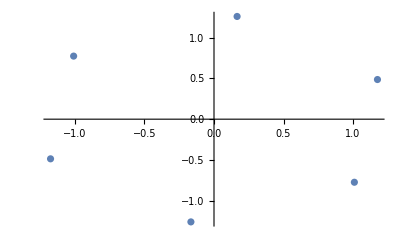

```mathematica
ListPlot[a]
```

Ritade en circkel som paserar alla 6 punkter med hjälp av ritnningsverktyg i Mathematica sedan plotade en cirkel, och sen  med hjläp av funktionen Show  plotade cirkeln och föregånde graph som visar hur de samtliga lösningar till ekvationen bildar en cirkel.

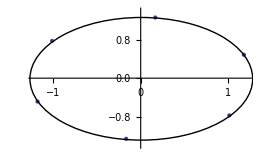

```mathematica
f
```

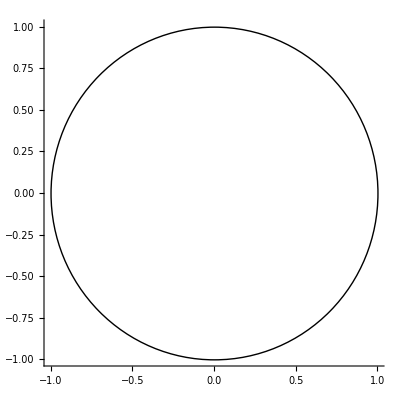

ListPlot::lpn: ListOfPoints is not a list of numbers or pairs of numbers.

PlotRange::argx: PlotRange called with 2 arguments; 1 argument is expected.

```mathematica
e=Graphics[Circle[],Axes->True,AxesOrigin->Automatic]
```

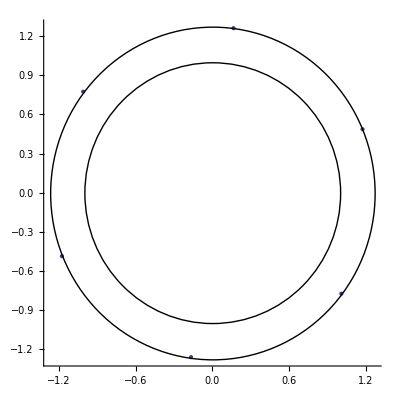

ListPlot::lpn: ListOfPoints is not a list of numbers or pairs of numbers.

```mathematica
Show[e,f]
```

```mathematica
Show[e,f]
```

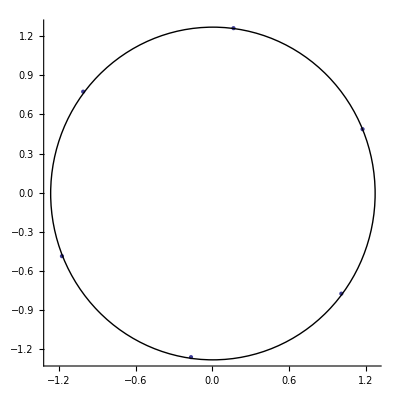

Logic:
1) 
        B) Vilka av dessa propositioner är sanna?

```mathematica
p1: (√2∈ℝ)∧∼(√2∈Q)
```

```mathematica
FullSimplify[Element[√2,Reals]&& !Element[√2,Rationals]]
```

True

```mathematica
p2: 1/2 ∈ Z ∨ 1/2∈Q 
FullSimplify[Element[1/2,Integers]∨ Element[1/2,Rationals]]
```

p2:1/2∈Z||1/2∈Q

True

```mathematica
p3:~(-4∈N)⟶~(-4∈Z)
```

```mathematica
Implies[!NonNegative[-4],!Element[-4,Integers]]
```

False

```mathematica
p4: 2.5∈Q↔ 2.5∈R
```

Element::argrx: Element called with 3 arguments; 2 arguments are expected.

```mathematica
Equivalent[Element[5/2,Rationals],Element[2.5,Reals]]
```

True

Ekvationlösning och grafer: 

En D’Artagnan jagas av Richeliue. Båda rider så snabbt de kan. D’Artagnan rider med en hastighet av 42 km/h och Richeliue med 57 km/h. Richeliue är 60 meter efter D’Artagnan och det är 250 meter till stadsporten där D’Artagnan kan komma undan. Bestäm om Richeliue hinner i kapp D’Artagnan och i så fall vilken tidpunkt och sträcka innan stadsporten det sker. Illustrera tidsförloppet grafiskt på lämpligt sätt.

Show::gcomb: Could not combine the graphics objects in .